# SU(2)超自由度光的可视化

```mathematica
SetDirectory["B:\\Lee\\Research\\Pictures\\"];
<<Notation`
<<MATLink`
OpenMATLAB[]
```

## 参数定义及含义

#### Ω：模式间隔比

```mathematica
Ω==Δ Subscript[f, T]/Δ Subscript[f, L]==P/Q
```

取值范围

根据腔稳条件，腔长须满足0<L<R，故Ω∈[0,1/2]

#### 平凹腔，模式间隔比 与 腔长 的关系

```mathematica
L/R==sin^2(Ωπ)
```

Ω：模式间隔比

L/R：腔长

## 波迹二象性

#### 轨迹性：M>0【n_0影响光场范围】

SU(2)简并态/SU(2)相干态模/平面几何模，此时为对应于经典轨道的不同阶数的SU(2)相干态波包

#### 波动性：M=0

非简并态，此时为HG模【谐振子的本征态波包】

#### 简并态【频率简并谐振腔】

谐振腔的本征频率，与横。纵模频率间隔均有关

```mathematica
Subscript[Δf, L]=c/(2L)
Subscript[Δf, T]=(Subscript[Δf, L] ϑ(L))/π
Subscript[f, n,m,s]=s·Subscript[Δf, L]+(n+m+1)·Subscript[Δf, T]
```

频率简并性：同一本征频率可用不同的横、纵阶数组成

定义模式间隔比

```mathematica
Ω=Subscript[Δf, T]/Subscript[Δf, L]=P/Q
```

### 参数

#### M：阶数

越小，波动性越强，越容易展现相干条纹；
越大，轨迹性越强，越容易坐落在分立轨道上。

#### n_0：光束模场范围

越大，光束范围越大，反之越小

#### ϕ：相干态相位

可调节ϕ表现波动性，某些ϕ下的轨道交叉可引起相干叠加、产生波动条纹。

-Graphics-

## Lissajous曲线

### 1. 仅改变x方向

```mathematica
TabView[{"参数式"->"x=A_xsin(ω_xt+δ_x) | y=sin(t) | 0≤t≤2 π\n\nω_x: horizontal angular frequency\nδ_x: horizontal angular phase\nA_x: horizontal amplitude"}]//TraditionalForm
```

1

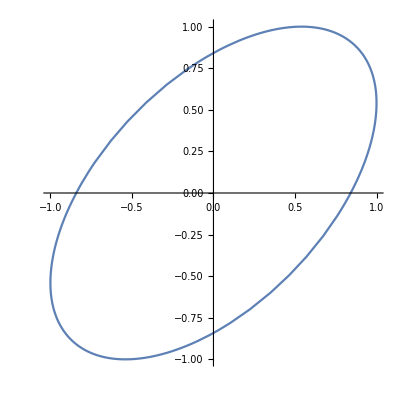

```mathematica
FormFunction[{{"ωx","ω_x: horizontal angular frequency"}->"Number"->1,{"δx","δ_x: horizontal angular phase"}->"Number"->1,{"Ax","A_x: horizontal amplitude"}->"Number"->1},ParametricPlot[{#Ax Sin[#ωx t+#δx],Sin[t]},{t,0,2π}]&,AppearanceRules-><|"Title"->"Lissajous Curve","Description"->"Enter A_x, ω_x and δ_x to visulize the curve"|>][]
```

### 2. xy方向都改变

```mathematica
TabView[{"参数式"->"x=A_xsin(ω_xt+δ_x) | y=A_y sin(ω_y t+δ_y) | 0≤t≤2 π\n\nω: Angular frequency\nδ: Angular phase\nA: Amplitude"}]//TraditionalForm
```

1

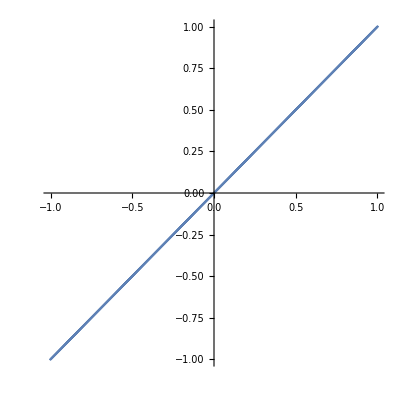

```mathematica
FormFunction[{{"ωx","ω_x: horizontal angular frequency"}->"Number"->1,{"ωy","ω_y: vertical angular frequency"}->"Number"->1,{"δx","δ_x: horizontal angular phase"}->"Number"->1,{"δy","δ_y: vertical angular phase"}->"Number"->1,{"Ax","A_x: horizontal amplitude"}->"Number"->1,{"Ay","A_y: vertical amplitude"}->"Number"->1},ParametricPlot[{#Ax Sin[#ωx t+#δx],#Ay Sin[#ωy t+#δy]},{t,0,2π}]&,AppearanceRules-><|"Title"->"Lissajous Curve","Description"->"Enter A, ω and δ to visulize the curve"|>][]
```

```mathematica
<<MATLink`
OpenMATLAB[]
```

MATLink::needs: MATLink is already loaded. Remember to use Needs instead of Get.

OpenMATLAB::wspo: The MATLAB workspace is already open.

x=-3.5:0.2:3.5;
y=x;
[X,Y]=meshgrid(x,y);
z=X.*exp(-X.^2-Y.^2);
subplot(1,3,1)
mesh(z)
subplot(1,3,2)
meshc(z)
subplot(1,3,3)
surf(z)

#### 理解shading interp

shading阴影函数控制曲面和图形对象的颜色着色，用来处理色彩效果，包括三种形式

shading faceted：默认，在曲面或图形对象上叠加黑色的网格线
shading flat：在黑色网格线基础上，去掉图上的网格线
shading interp：对图形进行色彩的插值处理，使得色彩平滑过渡

subplot(2,2,1)
sphere(20);
title("默认")

subplot(2,2,2)
sphere(20);
shading faceted
title("shading faceted即默认")

subplot(2,2,3)
sphere(20);
shading flat
title("shading flat取消黑色网格线")

subplot(2,2,4)
sphere(20);
shading interp
title("shading interp：色彩平滑过渡")

#### View

sphere(100)
shading interp
light("Position",[1,3,2])
light("Position",[-1,-3,-2])
material shiny
axis vis3d off

#### Lighting

光照算法

lighting flat：均匀分布的光照【类似于shading flat】，选择此法可查看分娩着色的对象
lighting gouraud：计算顶点法向量，并向各个面中线性插值【类似于shading interp】
lighting none
lighting(ax,..)使用ax指定的坐标区域，而非当前坐标区域

light对象对当前做鱼区域中的所有surface和patch对象的影响的算法。要使lighting命令起作用，必须用light或lightangle函数创建一个光照对象。

如，下面没有用light或lightangle创建光照对象，故lighting函数没用

close all
sphere(100)
shading interp

close all
sphere(100)
shading interp
light("Position",[1,3,2])
lighting gouraud

试一下lighting phong

close all
subplot(1,2,1)
sphere(50)
shading interp
light("Position",[1,2,3])
lighting flat

subplot(1,2,2)
sphere(50)
shading interp
light("Position",[1,2,3])
lighting gouraud

默认无光照

sphere
axis equal

close all
figure(10)
sphere
axis equal
light("Position",[1,2,3])
lighting none

figure
	subplot(1,3,1)
	sphere
	light("Position",[1,2,3])
	lighting flat
	subplot(1,3,2)
	sphere
	lighting flat
	subplot(1,3,3)
	sphere
	lighting flat

#### shading需要先用light & lightangle创建光照对象吗？

figure
subplot(1,3,1)
sphere(20)
shading interp

subplot(1,3,2)
sphere(20)
light("Position",[1,2,3])
shading interp

clc
	clear all
	close all
	figure()
	subplot(2,3,1)
	sphere
	light("Position",[1,2,3])
	lighting flat
	
	subplot(2,3,2)
	sphere
	lighting flat
	
	subplot(2,3,3)
	sphere

	subplot(2,3,4)
	sphere
	light("Position",[2,3,3])
	shading interp	
	
	subplot(2,3,5)
	sphere
	shading interp
	
	subplot(2,3,6)
	sphere

证明：shading不要求先用light & lightangle创建光照对象

#### axis tight

t = 0:0.1:2*pi;
x = 3*cos(t);
y = sin(t);

subplot(2,2,1);plot(x,y);axis normal
subplot(2,2,2);plot(x,y);axis square
subplot(2,2,3);plot(x,y);axis equal
subplot(2,2,4);plot(x,y);axis tight

t = 0:0.1:2*pi;
x = 3*cos(t);
y = sin(t);

subplot(2,2,1);plot(x,y);axis tight
subplot(2,2,2);plot(x,y);axis square
subplot(2,2,3);plot(x,y);axis tight square
subplot(2,2,4);plot(x,y);axis tight equal

#### 设置lightangle

#### 设置view

sphere
view(90,90)

sphere(50);
shading interp;
view(45,45)

-Graphics-

转为MMA代码，需要查一下Module和Block

```mathematica
SystemOpen["http://blog.sciencenet.cn/blog-531885-598318.html"]
```

子函数【用Module定UI的函数】与Matlab中定义的函数没有什么区别。Block也能实现，但不知二者之间的区别。

```mathematica
f1[x_,y_]:=Module[{A},A=x^2+y^2]
f1[1,1]
```

2

```mathematica
f1[1,1]
```

2

```mathematica
f2[x_,y_]:=Module[{A},A=x^2+y^2;Return[A+1]]
```

```mathematica
f2[1,1]
```

3

#### 1. With

局部变量必须赋初值

2. 不可在expr中再被赋值

```mathematica
With[{},]
```

```mathematica
x=.;n=2;
(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2),{x,n}]
```

ⅇ^(x^2) (-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2)

Never用Module较多

-Graphics-

-Graphics-

#### 那MMA程序包用的编程语言和MMA语言一样吗？

北京 物理 Runge
一样
wolfram language
但也不一定，mma也能混合编程
*wl

#### 对 我就想问*wl中用的什么编程语言

源代码的话是一样的。不过wl文件里可能存的是经Encoded加密了的代码

```mathematica
D[ⅇ^(-x^2),{x,2}]
```

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

#### matlabFunctiom

help matlabFunction

将符号表达式转换成function handle

syms x y
r=sqrt(x^2+y^2);
ht=matlabFunction(r)

ht =

  function_handle with value:

    @(x,y)sqrt(x.^2+y.^2)

```mathematica
<<MATLink`
```

MATLink::needs: MATLink is already loaded. Remember to use Needs instead of Get.

function H = H_gen(n,x)
	syms xx
	Hn=(-1)^n*exp(xx^2)*diff(exp(-xx^2),xx,n);
	f=matlabFunction(Hn);
if n==0
	H=1;
else
	H=f(x);
end

#### 实现方法1

```mathematica
Clear["Global`*"]
Hn[n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2),{x,n}];
Hgen[n_,x_]:=If[n==0,H=1,H=Hn[n,x]];
Hgen[2,6]
```

142

加上Return[H]有没有区别？

```mathematica
Clear["Global`*"]
Hn[n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2),{x,n}];
Hgen[n_,x_]:=If[n==0,H=1,H=Hn[n,x],Return[H]];
Hgen[2,6]
```

142

#### 方法2

```mathematica
Clear["Global`*"]
Hn[n_,x_]:=(-1)^n ⅇ^(x^2)(D[ⅇ^(-t^2),{t,n}]/.t->x);
Hgen[n_,x_]:=If[n==0,H=1,H=Hn[n,x]]
Hgen[2,6]
```

142

#### 把H=都去掉

```mathematica
Clear["Global`*"]
Hn[n_,x_]:=(-1)^n ⅇ^(x^2)(D[ⅇ^(-t^2),{t,n}]/.t->x);
Hgen[n_,x_]:=If[n==0,1,Hn[n,x]]
Hgen[2,6]
```

142

#### 写n阶导的漂亮形式

```mathematica
D[f[x],{x,n}]//HoldForm
```

∂_{x,n} f[x]

```mathematica
D[f[x], {x,2}]
```

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

```mathematica
Hn[n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2), {x,n}];
Subscript[ℋ, gen][n_,x_]:=If[n==0,H=1,H=Hn[n,x]];
Subscript[ℋ, gen][2,6]
```

142

#### 写1,2阶导的漂亮形式

```mathematica
Subscript[ℋ, 𝓃][n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2), {x,2}]
```

(-1)^n ⅇ^(x^2) (-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2)

```mathematica
g[x_]:=ⅇ^(-x^2);
Subscript[ℋ, 𝓃][x_]:=(-1)^2 ⅇ^(x^2)g''[x]
Subscript[ℋ, 𝓃][6]
```

142

#### 方法3

```mathematica
Clear["Global`*"];
Subscript[ℋ, gen][n_,x_]:=Module[{},Subscript[ℋ, 𝓃][n,x]=(-1)^m ⅇ^(t^2)D[ⅇ^(-t^2), {t,m}]/.{m->n,t->x};If[n==0,H=1,H=Subscript[ℋ, 𝓃][n,x]];Return[H]]
```

```mathematica
Subscript[ℋ, gen][2,6]
```

142

#### 为何要使用Return?

原因之一：因为写了H=1等，所以要写Return

#### 为何Module的{}中不写{n,x}?

因为内部参数不能与外部输入参数相同

```mathematica
Clear["Global`*"];
Subscript[ℋ, gen][n_,x_]:=Module[{n,x},Subscript[ℋ, 𝓃][n,x]=(-1)^m ⅇ^(t^2)D[ⅇ^(-t^2), {t,m}]/.{m->n,t->x};If[n==0,H=1,H=Subscript[ℋ, 𝓃][n,x]];Return[H]]
Subscript[ℋ, gen][2,6]
```

Module::lvsym: Local variable specification {2,6} contains 2, which is not a symbol or an assignment to a symbol.

Module[{2,6},ℋ_𝓃[2,6]=(-1)^m ⅇ^(t^2) ∂_{t,m} ⅇ^(-t^2)/.{m→2,t→6};If[2==0,H=1,H=ℋ_𝓃[2,6]];Return[H]]

#### 内部参数不能与外部输入参数相同吗？

即，全局变量与局部变量作用域不同

{n,x}是局部变量，若局部变量与输入参数同名，计算机将难以识别

数学中的映射角度来说的话，我们最希望的是一对一映射---一个萝卜一个坑 
如果一个坑里多个萝卜，发生在计算机上，那将很难识别。。。。

另一个人的答案“MMA code很少见有用到Return，module的含义就是要用局部变量，你在Arguments里面已经有了n,x了，不需要再弄这些，逻辑上很多都是不必要的。

康小广：要是不加Return，会改变函数的返回值。Hgen[x,y]本来返回H，不加就返回Null

```mathematica
f[x0_]:=Module[{x=x0},While[x>0,x=Log[x]];x]
f[2]
```

Log[Log[2]]

```mathematica
Clear["Global`*"];
Subscript[ℋ, gen][n_,x_]:=Module[{},Subscript[ℋ, 𝓃][n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2), {x,n}];If[n==0,1,Subscript[ℋ, 𝓃][n,x]]]
Subscript[ℋ, gen][2,6]
```

RuleDelayed::rhs: Pattern n_ appears on the right-hand side of rule ℋ_gen[n_,x_]:>Module[{},ℋ_𝓃[n_,x_]=(-1)^n ⅇ^(x^2) ∂_{x,n} ⅇ^Times[«2»];If[n==0,1,ℋ_𝓃[n,x]]].

RuleDelayed::rhs: Pattern x_ appears on the right-hand side of rule ℋ_gen[n_,x_]:>Module[{},ℋ_𝓃[n_,x_]=(-1)^n ⅇ^(x^2) ∂_{x,n} ⅇ^Times[«2»];If[n==0,1,ℋ_𝓃[n,x]]].

General::ivar: 6 is not a valid variable.

Pattern::patvar: First element in pattern Pattern[2,_] is not a valid pattern name.

Pattern::patvar: First element in pattern Pattern[6,_] is not a valid pattern name.

ⅇ^36 ∂_{6,2} 1/ⅇ^36

一样的原因：外面已经有ℋ_gen[n_,x_]了，里面就不能再写ℋ_𝓃[n_,x_]

换句话说：n,x用的很乱，两个函数用一个符号

```mathematica
Clear["Global`*"];
Subscript[ℋ, gen][n_,x_]:=Module[{},Subscript[ℋ, 𝓃][n1_,x1_]=(-1)^n1 ⅇ^(x1^2)D[ⅇ^(-x1^2), {x1,n1}];If[n==0,1,Subscript[ℋ, 𝓃][n,x]]]
Subscript[ℋ, gen][2,6]
```

ⅇ^36 ∂_{6,2} 1/ⅇ^36

但这样还是达不到需要的效果

#### 纯函数求导的方法

```mathematica
f[x_]:=ⅇ^(-x^2)
f'[x]/.x->2
f'[2]
```

-4/ⅇ^4

-4/ⅇ^4

#### ...

一般把自定义的函数放在外面，

#### MMA保存为矢量图

```mathematica
Export["1.svg",ParametricPlot[{Sin[u] u,Cos[u] u},{u,0,100}]]
```

1.svg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1.svg"]]]
```

svg: Scalable Vector Graphics

cvgmt：现在只有2D的pdf才是矢量图，3D图都栅格化了。pdf并不是一个存储矢量图合适的工具（即便Adobe有自己的PRC 3D格式，且也支持嵌入的u3d格式），还是等MMA的WebGL吧。

为何是PDF  我看知乎上说保存为svg是矢量图？

2D 的话，pdf 和 svg MMA 默认  输出的都是向量图。

如果是处理 3D，svg 更不行，svg 本来只是一个 2D  的格式。

pdf 貌似是mma输出效果最好的;eps svg 貌似都比pdf差一些

eps 和 svg 这两种语言的优势是容易提取里面的数据，所以容易裁剪。
pdf 这种编程语言加了很多特性，处理起来很复杂，基本上很难用记事本打开编辑。

```mathematica
Export["1.pdf",ParametricPlot[{Sin[u] u,Cos[u] u},{u,0,100}]]
```

1.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1.pdf"]]]
```

```mathematica
Export["1.eps",ParametricPlot[{Sin[u] u,Cos[u] u},{u,0,100}]]
```

1.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1.eps"]]]
```

#### 保存的图如何去白边

```mathematica
PlotRangePadding->True
```

#### 保存为矢量图

要么选择.svg，但总得来说.pdf效果最好

```mathematica
Export["1.svg",ParametricPlot[{Cos[2u],Sin[u]},{u,0,10}]]
```

1.svg

```mathematica
SystemOpen["1.svg"]
```

```mathematica
Export["1.pdf",ParametricPlot[{Cos[2u],Sin[u]},{u,0,10}]]
```

1.pdf

```mathematica
SystemOpen["1.pdf"]
```

## 代码工程

### 理论推导

SU(2)相干态的表达式

p_101 公式(5-87)

-Graphics-

-Graphics-

-Graphics-

取HG模的

```mathematica
Symbolize[Subscript[ϕ, 0]]
```

```mathematica
Notation[Subscript[ψ, Subscript[n, 0]]^M(x,y,z,Subscript[ϕ, 0]|Ω) ⟹ □]
```

```mathematica
1/2^(M/2)∑_(K=0)^M √((M!)/(K!(M-K)!))ⅇ^(ⅈ K Subscript[ϕ, 0])
```

波前曲率半径项多余

```mathematica
Symbolize[Subscript[Φ, n,m]^(HG)];Symbolize[Subscript[w, 0]];Symbolize[Subscript[Δf, T]];Symbolize[Subscript[Δf, L]];Symbolize[z̃]
```

注：ML中也有Hermite多项式

hermiteH(2,2)

ans =

    14

## 2. 频率简并谐振腔

#### 谐振腔的本征模频率为

非频率简并谐振腔

```mathematica
Symbolize[Subscript[Δf, L]];
Symbolize[Subscript[Δf, T]];
Subscript[Δf, L]=3;
Subscript[Δf, T]=5;
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
Subscript[f, 1,1,1]
```

18

光腔本征模谐振频率与横纵模均有关

与n,m,s均有关

#### 频率简并性

定义：同一本征频率可由不同的横纵模阶组合而成

类比简并：同样能量，不同轨道，即能量简并
频率简并：同样频率，不同横纵摸阶数，即频率简并

#### 模式间隔比

更重要横纵模间隔的相对大小

平凹腔，间隔比与腔长的关系

```mathematica
Subscript[Δf, L]=3;
Subscript[Δf, T]=5;
Notation[Ω ⟺ Subscript[Δf, T]/Subscript[Δf, L]]
Ω
```

5/3

```mathematica
P=3;
Q=5;
Notation[Ω ⟺ P/Q]
Ω
```

3/5

由传输矩阵论，得平凹腔中的Ω为

```mathematica
L=3;
R=4;
Notation[Subscript[z, R] ⟺ √(L(R-L))]
Subscript[z, R]
Notation[Ω ⟺ 1/π ArcTan[L/Subscript[z, R]]]
Ω
```

√3

1/3

```mathematica
L=3;
R=4;Notation[Ω ⟺ 1/π ArcCos[√(1-L/R)]]
Ω
```

1/3

上式等价于

```mathematica
Solve[L/R==Sin[Ωπ]^2,Ω]//Column
```

{Ω→ConditionalExpression[(-ArcSin[(√L)/(√R)]+2 π C[1])/π, C[1]∈ℤ]}
{Ω→ConditionalExpression[(π-ArcSin[(√L)/(√R)]+2 π C[1])/π, C[1]∈ℤ]}
{Ω→ConditionalExpression[(ArcSin[(√L)/(√R)]+2 π C[1])/π, C[1]∈ℤ]}
{Ω→ConditionalExpression[(π+ArcSin[(√L)/(√R)]+2 π C[1])/π, C[1]∈ℤ]}

#### 腔稳条件

根据谐振腔稳定性条件，腔长须满足0<L<R，故Ω∈[0,1/2]

改写下式

```mathematica
Subscript[f, n,m,s]==s·Δ Subscript[f, L]+(n+m+1)·Δ Subscript[f, T]
```

改写后的形式

```mathematica
Subscript[f, n,m,s]==[s+(n+m+1)·Ω]Δ Subscript[f, L]==[s+(n+m+1)·P/Q]Δ Subscript[f, L]
```

#### 频率简并的必要条件

```mathematica
Ω==P/Q∈ℚ
```

即，P与Q互素

#### Δf_T/Δ f_L==P/Q的关系？

Δ f_T，Δf_L不一定是整数，P,Q是对Δf_T/Δ f_L其有理化后的整数

```mathematica
Rationalize[0.21]
```

21/100

-Graphics-

答：这是产生频率简并的必要条件，而非直接由该式得到的结果。

#### 描述频率简并性

自变量：L/R

谱：Δf_(n,m,s)/Δ f_L

```mathematica
Ω=1/π ArcCos[√(1-L/R)]
```

```mathematica
Subscript[f, n,m,s]=(s+(n+m+1)×P/Q)Δ Subscript[f, L]
```

```mathematica
Ω=P/Q
```

P/Q

```mathematica
Subscript[f, n,m,s]=(s+(n+m+1)/π ArcCos[√(1-L/R)])Δ Subscript[f, L]
```

Δ (s+((1+m+n) ArcCos[√(1-L/R)])/π) f_L

令L/R=t

```mathematica
Subscript[f, n,m,s]=(s+(n+m+1)/π ArcCos[√(1-t)])Subscript[Δf, L]
```

```mathematica
Subscript[f, n,m,s]/Subscript[Δf, L]=s+(n+m+1)/π ArcCos[√(1-t)]
```

为了方便绘图，令(f_(n,m,s))/Δf_L≡𝒻_(n,m,s)

```mathematica
<<Notation`
```

```mathematica
Clear["Global`*"]
t=0.1
ArcCos[√(1-t)]
Notation[Subscript[𝒻, n_,m_,s_] ⟺ s_+(n_+m_+1)/π ArcCos[√(1-t)]]
Subscript[𝒻, 1,1,1]
```

0.1

0.321751

1.30725

参数范围：5≤s≤15，0≤m+n≤20

要看到频率简并点的分布情况，需要将多条线画到同一张图中

用Do函数

```mathematica
SystemOpen["B:\\Lee\\Research\\GroupMeeting\\2020.09\\shen's code of SU(2)【confidential】\\Simulation\\频率简并谱图.svg"]
```

```mathematica
SystemOpen["B:\\Lee\\Research\\GroupMeeting\\2020.09\\shen's code of SU(2)【confidential】\\Simulation\\频率简并谱图.pdf"]
```

则可看到频率简并点的分布，箭头为各频简态对应的Ω值

#### 频率简并态Ω=P/Q

腔态叫频简态

谐振腔态叫频率简并态

产生对应频率简并的谐振腔态叫频率简并态

#### 频简腔

产生简并态/简并腔的必要条件：Ω==P/Q∈Q

产生频率简并谐振腔的腔

#### 发射SU(2)简并态模式的简并腔

满足简并腔的必要条件Ω==P/Q∈Q不一定可发射SU(2)简并模式

无理数>有理数，简并态的产生条件 苛刻 非简并态

Ω：作为分数，越复杂越难激发。故简并态对应的腔参数可构成了一个.93魔鬼阶梯.94，一旦某简并态被激发,对应的模式发射将伴随明显的强度增加。

### 2. 横纵模耦合

简并腔可产生怎样的光子波包?

Chapter 2: 用双离轴泵浦控制横模阶数：控制一个方向的离轴量以控制一个方向的橫模阶数

若将此法用至频简腔，由于频简效应，纵模阶数同时会受到调制来保证频率简并

```mathematica
Subscript[f, n,m,s]==[(Subscript[s, 0]-PK)+(Subscript[n, 0]+QK+1)·P/Q]Δ Subscript[f, L]==[Subscript[s, 0]+(Subscript[n, 0]+1)·P/Q]Δ Subscript[f, L]
```

```mathematica
Symbolize[Subscript[n, 0]]
Symbolize[Subscript[s, 0]]
Symbolize[Subscript[Δf, L]]
```

```mathematica
Subscript[Δf, L]
```

1

```mathematica
Subscript[s, 0]=1
```

1

```mathematica
(Subscript[s, 0]+(Subscript[n, 0]+1)×P/Q)×Subscript[Δf, L]
```

5/3

```mathematica
Head[Subscript[s, 0]]
```

Symbol

```mathematica
Symbolize[Subscript[Δf, L]];
P=1;
Q=3;
Subscript[Δf, L]=1;
Notation[Subscript[f, n_,s_] ⟺ (s_+(n_+1)P/Q)Subscript[Δf, L]]
Subscript[f, 1,1]
```

5/3

#### N==s_0+n_0：守恒的玻色量子数

s_0和n_0：固定的纵模和横模阶数，则总阶数为守恒量

对应SU(2)相干态中守恒的玻色量子数

## 波迹二象性

#### 定义

频率简并腔的激光模式具有波迹二象性：当简并态被激发，激光模式趋于轨迹性；当非简并态被激发，趋于波动性

#### 简并激发下的轨迹性

理解：什么叫简并模式Ω=P/Q，若P,Q互素，则为简并模式

轨迹性：离轴泵浦光学腔中，一旦SU(2)简并态被激发，激光模式趋向于表现为周期光线轨迹，用ABCD传输矩阵描述

对于Ω=P/Q平凹简并腔，用平凹腔的ABCD矩阵和下式，可得平凹腔的ABCD矩阵

```mathematica
L/R==sin^2(Ωπ)
```

平凹腔的ABCD矩阵

```mathematica
A==({{1-(2L)/R, 2L(1-L/R)}, {-2/R, 1-(2L)/R}})==({{cos(2Ωπ), R/2 sin^2(2Ωπ)}, {-2/R, cos(2Ωπ)}})
```

则n次往返后的传输矩阵为

```mathematica
A^n==({{cos(2nΩπ), R/2 sin^2(2nΩπ)}, {-2/R(sin(2nΩπ))/(sin(2Ωπ)), cos(2nΩπ)}})
```

由于cos(2QΩπ)==cos(2Pπ)==1，sin(2QΩπ)==sin(2Pπ)==0，故经过Q次往返杜越对应的传输阵为单位阵

```mathematica
A^Q==({{cos(2QΩπ), R/2 sin^2(2QΩπ)}, {-2/R(sin(2QΩπ))/(sin(2Ωπ)), cos(2QΩπ)}})==I
```

在|Ω==P/Q⟩的简并腔中，稳定振荡光线经过Q次往返渡越将回到起点，设起点在平面镜处，发射光线垂直于平面镜(对应条件ϕ_0=0),

对应Ω=1/4和Ω=1/3简并腔的轨道绘制于下

```mathematica
Rasterize[-Graphics-,RasterSize->200]
```

-Graphics-

#### 非简并激发下的波动性

...

## 失败的尝试

```mathematica
Symbolize[Subscript[ω, 0]]
Symbolize[Subscript[𝓏, ℛ]]
Symbolize[Subscript[L, 𝒸]]
Symbolize[Subscript[𝓃, 0]]
Symbolize[Subscript[𝓂, 0]]
Symbolize[Subscript[ϕ, 0]]
Symbolize[Subscript[𝒫, 𝓋]]
Symbolize[Subscript[ℋ, 𝓃]]
Symbolize[Subscript[ℋ, gen]]
Symbolize[Subscript[ℋ𝒢, beam]]
Symbolize[Subscript[SU, 2]]
Symbolize[Subscript[𝓂, 1]]
```

```mathematica
ClearAll["Global`*"]
(*频率简并态*)
P=1;
Q=4;
λ=1050×10^-9;
Subscript[ω, 0]=50×10^-6;
k=(2π)/λ;
Subscript[𝓏, ℛ]=(π Subscript[ω, 0]^2)/λ;
Subscript[L, 𝒸]=Subscript[𝓏, ℛ] Tan[π(P/Q)];
z=Subscript[L, 𝒸];
R=z+Subscript[𝓏, ℛ]^2/z;
w=Subscript[ω, 0] √(1+(z/Subscript[𝓏, ℛ])^2);
ℒ=10w;

(*二维谐振子参数*)
p=-1;
q=Q-p;

Subscript[𝓃, 0]=20;
Subscript[𝓂, 0]=30;
𝒩=5;
Subscript[ϕ, 0]=π/2;
(*摆线*)
α=π/2;
β=π/2;
Subscript[𝒫, 𝓋]=0;
(*定义Subscript[ℋ, gen][n,x]*)
Subscript[ℋ, 𝓃][n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2), {x,n}];
Subscript[ℋ, gen][n_,x_]:=Piecewise[{{1, n==0}, {Subscript[ℋ, 𝓃][n,x], True}}]
(*Subscript[定义ℋ𝒢, gen][n,x]*)
Subscript[ℋ𝒢, beam][n_,m_,x_,y_,w_,k_,z_]:=(√(2/(π×m!×n!))2^(-(m+n)/2))/w Subscript[ℋ, gen][n,(√2)/(w×x)]Subscript[ℋ, gen][m,(√2)/(w×y)] ⅇ^(-(x^2+y^2)/w^2)ⅇ^(ⅈ(k(z+(x^2+y^2)/(2R))-(m+n+1)ArcTan[z/Subscript[𝓏, ℛ]]))
(*Subscript[定义SU, 2]*)
Subscript[SU, 2][n_,m_,x_,y_,w_,k_,z_,α_,β_]:=Module[{},Subscript[ℋ, LG]=0;N=n+m;Do[d=0;Do[d=d+(-1)^v(Cos[β/2]^(𝒩-n+Subscript[𝓂, 1]-2v)Sin[β/2]^(n-Subscript[𝓂, 1]+2v))/(v!(𝒩-n-v)!(Subscript[𝓂, 1]-v)!(n-Subscript[𝓂, 1]+v)!),{v,Max[0,Subscript[𝓂, 1]-n],Min[𝒩-n,Subscript[𝓂, 1]]}];d=√(Subscript[𝓂, 1]!(𝒩-Subscript[𝓂, 1])!n!(𝒩-n)!)d;Subscript[ℋ, LG]=Subscript[ℋ, LG]+ⅇ^(-ⅈ×Subscript[𝓂, 1] α)d×Subscript[ℋ𝒢, beam][Subscript[𝓂, 1],𝒩-Subscript[𝓂, 1],x,y,w,k,z],{Subscript[𝓂, 1],0,𝒩}]]
(*Subscript[定义𝒫, 𝓋]*)
Do[m=Subscript[𝓂, 0]+q×K;n=Subscript[𝓃, 0]+p×K;Subscript[𝒫, 𝓋]=Subscript[𝒫, 𝓋]+((√((𝒩!(𝒩-K))/K!)ⅇ^(ⅈK Subscript[ϕ, 0]))/2^(𝒩/2))Subscript[SU, 2][n,m,x,y,w,k,z,α,β],{K,0,𝒩}];
DensityPlot[Subscript[𝒫, 𝓋]//N,{x,-10*Subscript[ω, 0],10*Subscript[ω, 0]},{y,-10*Subscript[ω, 0],10*Subscript[ω, 0]}]
```

#### 用//N比较Matlab和MMA计算的数值

```mathematica
OpenMATLAB[]
```

m1=15;
n=2;
m=30;
d=5;
d=(factorial(m1)*factorial(n+m-m1)*factorial(n)*factorial(m))^0.5*d

d =

   2.4837e+30

```mathematica
Subscript[𝓂, 1]=15;
n=2;
m=30;
d=5;
𝒩=n+m;
d=√(Subscript[𝓂, 1]!(𝒩-Subscript[𝓂, 1])!n!(𝒩-n)!)d//N
```

2.4837×10^30

#### Matlab是浮点数值运算，有误差

cos(pi/2)

ans =

   6.1232e-17

```mathematica
Cos[π/2]
```

0

```mathematica
ClearAll["Global`*"]
(*频率简并态*)
P=1;
Q=4;
λ=1050×10^-9;
Subscript[ω, 0]=50×10^-6;
k=(2π)/λ;
Subscript[𝓏, ℛ]=(π Subscript[ω, 0]^2)/λ;
Subscript[L, 𝒸]=Subscript[𝓏, ℛ] Tan[π(P/Q)];
z=Subscript[L, 𝒸];
R=z+Subscript[𝓏, ℛ]^2/z;
w=Subscript[ω, 0] √(1+(z/Subscript[𝓏, ℛ])^2);
ℒ=10w;

(*二维谐振子参数*)
p=-1;
q=Q-p;

Subscript[𝓃, 0]=20;
Subscript[𝓂, 0]=30;
𝒩=5;
Subscript[ϕ, 0]=π/2;
(*摆线*)
α=π/2;
β=π/2;
Subscript[𝒫, 𝓋]=0;
(*定义Subscript[ℋ, gen][n,x]*)
Subscript[ℋ, 𝓃][n_,x_]=(-1)^n ⅇ^(x^2)D[ⅇ^(-x^2), {x,n}];
Subscript[ℋ, gen][n_,x_]:=Piecewise[{{1, n==0}, {Subscript[ℋ, 𝓃][n,x], True}}]
(*Subscript[定义ℋ𝒢, gen][n,x]*)
Subscript[ℋ𝒢, beam][n_,m_,x_,y_,w_,k_,z_]:=(√(2/(π×m!×n!))2^(-(m+n)/2))/w Subscript[ℋ, gen][n,(√2)/(w×x)]Subscript[ℋ, gen][m,(√2)/(w×y)] ⅇ^(-(x^2+y^2)/w^2)ⅇ^(ⅈ(k(z+(x^2+y^2)/(2R))-(m+n+1)ArcTan[z/Subscript[𝓏, ℛ]]))
(*Subscript[定义SU, 2]*)
Subscript[SU, 2][n_,m_,x_,y_,w_,k_,z_,α_,β_]:=∑_(Subscript[𝓂, 1]=0)^(n+m) ∑_(v=Max[0,Subscript[𝓂, 1]-n])^min[m,Subscript[𝓂, 1]] (-1)^v(Cos[β/2]^(m+Subscript[𝓂, 1]-2v)Sin[β/2]^(n-Subscript[𝓂, 1]+2v))/(v!(m-v)!(Subscript[𝓂, 1]-v)!(n-Subscript[𝓂, 1]+v)!)



Module[Subscript[{},ℋ, LG]=0;N=n+m;Do[d=0;Do[d=d+(-1)^v(Cos[β/2]^(𝒩-n+Subscript[𝓂, 1]-2v)Sin[β/2]^(n-Subscript[𝓂, 1]+2v))/(v!(𝒩-n-v)!(Subscript[𝓂, 1]-v)!(n-Subscript[𝓂, 1]+v)!),{v,Max[0,Subscript[𝓂, 1]-n],Min[𝒩-n,Subscript[𝓂, 1]]}];d=√(Subscript[𝓂, 1]!(𝒩-Subscript[𝓂, 1])!n!(𝒩-n)!)d;Subscript[ℋ, LG]=Subscript[ℋ, LG]+ⅇ^(-ⅈ×Subscript[𝓂, 1] α)d×Subscript[ℋ𝒢, beam][Subscript[𝓂, 1],𝒩-Subscript[𝓂, 1],x,y,w,k,z],{Subscript[𝓂, 1],0,𝒩}]]
(*Subscript[定义𝒫, 𝓋]*)
Do[m=Subscript[𝓂, 0]+q×K;n=Subscript[𝓃, 0]+p×K;Subscript[𝒫, 𝓋]=Subscript[𝒫, 𝓋]+((√((𝒩!(𝒩-K))/K!)ⅇ^(ⅈK Subscript[ϕ, 0]))/2^(𝒩/2))Subscript[SU, 2][n,m,x,y,w,k,z,α,β],{K,0,𝒩}];
DensityPlot[Subscript[𝒫, 𝓋]//N,{x,-10*Subscript[ω, 0],10*Subscript[ω, 0]},{y,-10*Subscript[ω, 0],10*Subscript[ω, 0]}]
```

```mathematica
Subscript[Φ, n,m]^(HG)(x,y,z)==1/(√(2^(m+n-1)πm!n!))1/(w(z))Subscript[H, n][(√2 x)/(w(z))]Subscript[H, m][(√2 x)/(w(z))]exp[-(x^2+y^2)/(w^2(z))]
```